```mathematica
f[x_] = x^5-4*x^4-3*x^3+2*x+1
```

1+2 x-3 x^3-4 x^4+x^5

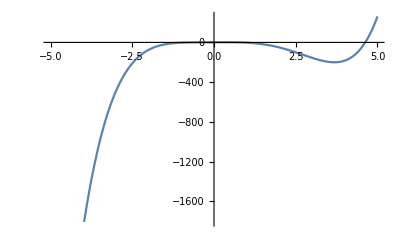

```mathematica
Plot[f[x],{x,-5,5}]
```

```mathematica
FindRoot[f[x],{x,-1}]
```

{x→-0.542726}

```mathematica
FindRoot[f[x],{x,1}]
```

{x→0.773907}

```mathematica
FindRoot[f[x],{x,4}]
```

{x→4.62611}

```mathematica
fi1[x_] =  (-(-4*x^4-3*x^3+2*x+1))^(1/5)
```

(-1-2 x+3 x^3+4 x^4)^(1/5)

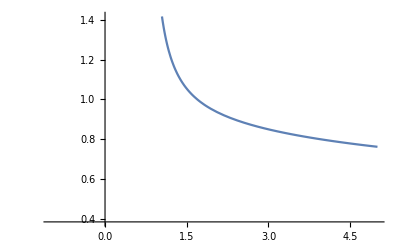

```mathematica
Plot[fi1'[x],{x,-1,5}]
```

```mathematica
fi1'[-0.54]
```

3.25089+2.36191 ⅈ

```mathematica
fi1'[0.77]
```

6.76206

```mathematica
fi1'[4.63]
```

0.774828